# Options evaluations

## Definitions

```mathematica
MkOption[aposition_, atype_, astrike_] := {position->aposition,type->atype,strike->astrike}
```

```mathematica
GetValue[option_, key_] := Replace[key, FilterRules[option,{key}][[1]]]
```

```mathematica
OptionPosition[option_] := Switch[ GetValue[option, position],
long, 1,
short, -1]
```

```mathematica
OptionPayoff[option_, price_]:= OptionPosition[option] * Switch[ GetValue[option, type],
call, Max[0, price - GetValue[option, strike]],
put, Max[0, GetValue[option, strike] - price]]
```

```mathematica
PortfolioPayoff[portfolio_, price_]:=Fold[Plus, 0, OptionPayoff[#, price]& /@portfolio ]
```

## Examples

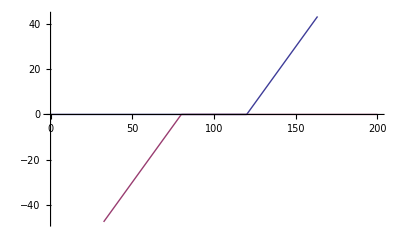

```mathematica
Plot[{OptionPayoff[MkOption[long, call, 120], S], OptionPayoff[MkOption[short, put, 80], S]}, {S, 0, 200}]
```

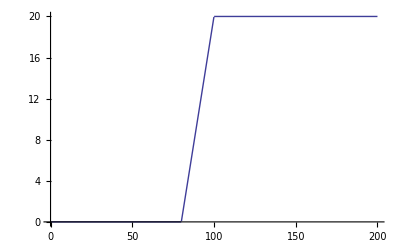

```mathematica
Plot[PortfolioPayoff[{MkOption[long, call, 80],MkOption[short, call, 100]}, S], {S, 0, 200}]
```